```mathematica
eqs={
p1+p2==2pa,
p3+p4==2pb,
p5+p6==2pc,
p7+p8==2pd,
q1-q2==2(p1-p2)ga,
q3-q4==2(p3-p4)gb,
q5-q6==2(p5-p6)gc,
q7-q8==2(p7-p8)gd,
q2+q3+q7==0,
q4+q5==0,
q1==0,
q6==0,
q8==0,
p2==p3==p7,
p4==p5
};
```

```mathematica
eqs/.{pa->10,pb->0,pc->0,pd->0,ga->1,gb->1,gc->1,gd->1}//Expand
Solve[%,{p1,p2,p3,p4,p5,p6,p7,p8,q1,q2,q3,q4,q5,q6,q7,q8}]//N
```

{p1+p2==20,p3+p4==0,p5+p6==0,p7+p8==0,q1-q2==2 p1-2 p2,q3-q4==2 p3-2 p4,q5-q6==2 p5-2 p6,q7-q8==2 p7-2 p8,q2+q3+q7==0,q4+q5==0,q1==0,q6==0,q8==0,p2==p3==p7,p4==p5}

{{p1→17.5,p2→2.5,p3→2.5,p4→-2.5,p5→-2.5,p6→2.5,p7→2.5,p8→-2.5,q1→0.,q2→-30.,q3→20.,q4→10.,q5→-10.,q6→0.,q7→10.,q8→0.}}

```mathematica
Power[1/(π/(8 1/1000)),0.25]
```

0.224639

```mathematica
(π r^4)/(8 1/1000 1)/.{r->0.225}
```

1.00644

```mathematica
{q1,q2,q3,q4,q5,q6,q7,q8}/.Solve[eqs,{p1,p2,p3,p4,p5,p6,p7,p8,q1,q2,q3,q4,q5,q6,q7,q8}]//Simplify
%[[1]]//MatrixForm
```

{{0,-(4 ga (gb (pa-pb)+gc (pa-2 pb+pc)+gd (pa-pd)))/(ga+gb+gc+gd),(4 (ga gb (pa-pb)+ga gc (pa-2 pb+pc)+gb gd (-pb+pd)+gc gd (-2 pb+pc+pd)))/(ga+gb+gc+gd),(4 gc (ga (pa-2 pb+pc)+gb (-pb+pc)+gd (-2 pb+pc+pd)))/(ga+gb+gc+gd),-(4 gc (ga (pa-2 pb+pc)+gb (-pb+pc)+gd (-2 pb+pc+pd)))/(ga+gb+gc+gd),0,(4 gd (ga (pa-pd)+gb (pb-pd)+gc (2 pb-pc-pd)))/(ga+gb+gc+gd),0}}

(0
-(4 ga (gb (pa-pb)+gc (pa-2 pb+pc)+gd (pa-pd)))/(ga+gb+gc+gd)
(4 (ga gb (pa-pb)+ga gc (pa-2 pb+pc)+gb gd (-pb+pd)+gc gd (-2 pb+pc+pd)))/(ga+gb+gc+gd)
(4 gc (ga (pa-2 pb+pc)+gb (-pb+pc)+gd (-2 pb+pc+pd)))/(ga+gb+gc+gd)
-(4 gc (ga (pa-2 pb+pc)+gb (-pb+pc)+gd (-2 pb+pc+pd)))/(ga+gb+gc+gd)
0
(4 gd (ga (pa-pd)+gb (pb-pd)+gc (2 pb-pc-pd)))/(ga+gb+gc+gd)
0)

```mathematica
Solve[eqs,{p1,p2,p3,p4,p5,p6,p7,p8,q1,q2,q3,q4,q5,q6,q7,q8}]//Simplify
```

{{p1→(ga pa+2 gb pa+2 gc pa+2 gd pa-gb pb-2 gc pb+gc pc-gd pd)/(ga+gb+gc+gd),p2→(ga pa+gb pb+2 gc pb-gc pc+gd pd)/(ga+gb+gc+gd),p3→(ga pa+gb pb+2 gc pb-gc pc+gd pd)/(ga+gb+gc+gd),p4→(-ga pa+2 ga pb+gb pb+2 gd pb+gc pc-gd pd)/(ga+gb+gc+gd),p5→(-ga pa+2 ga pb+gb pb+2 gd pb+gc pc-gd pd)/(ga+gb+gc+gd),p6→(-gb pb-2 gd pb+2 gb pc+gc pc+2 gd pc+ga (pa-2 pb+2 pc)+gd pd)/(ga+gb+gc+gd),p7→(ga pa+gb pb+2 gc pb-gc pc+gd pd)/(ga+gb+gc+gd),p8→(-ga pa-gb pb-2 gc pb+gc pc+2 ga pd+2 gb pd+2 gc pd+gd pd)/(ga+gb+gc+gd),q1→0,q2→-(4 ga (gb (pa-pb)+gc (pa-2 pb+pc)+gd (pa-pd)))/(ga+gb+gc+gd),q3→(4 (ga gb (pa-pb)+ga gc (pa-2 pb+pc)+gb gd (-pb+pd)+gc gd (-2 pb+pc+pd)))/(ga+gb+gc+gd),q4→(4 gc (ga (pa-2 pb+pc)+gb (-pb+pc)+gd (-2 pb+pc+pd)))/(ga+gb+gc+gd),q5→-(4 gc (ga (pa-2 pb+pc)+gb (-pb+pc)+gd (-2 pb+pc+pd)))/(ga+gb+gc+gd),q6→0,q7→(4 gd (ga (pa-pd)+gb (pb-pd)+gc (2 pb-pc-pd)))/(ga+gb+gc+gd),q8→0}}

```mathematica
Eliminate[eqs,{q1,q2,q3,q4,q5,q6,q7,q8}]
Solve[%,{p1,p2,p3,p4,p5,p6,p7,p8}]
```

ga p1==-gb p5-gc p5+gc p6+ga p7+gb p7+gd p7-gd p8&&p2==p7&&p3==p7&&p4==p5&&2 pa==p1+p7&&2 pb==p5+p7&&2 pc==p5+p6&&2 pd==p7+p8

{{p1→-(-ga pa-2 gb pa-2 gc pa-2 gd pa+gb pb+2 gc pb-gc pc+gd pd)/(ga+gb+gc+gd),p2→-(-ga pa-gb pb-2 gc pb+gc pc-gd pd)/(ga+gb+gc+gd),p3→-(-ga pa-gb pb-2 gc pb+gc pc-gd pd)/(ga+gb+gc+gd),p4→-(ga pa-2 ga pb-gb pb-2 gd pb-gc pc+gd pd)/(ga+gb+gc+gd),p5→-(ga pa-2 ga pb-gb pb-2 gd pb-gc pc+gd pd)/(ga+gb+gc+gd),p6→-(-ga pa+2 ga pb+gb pb+2 gd pb-2 ga pc-2 gb pc-gc pc-2 gd pc-gd pd)/(ga+gb+gc+gd),p7→-(-ga pa-gb pb-2 gc pb+gc pc-gd pd)/(ga+gb+gc+gd),p8→-(ga pa+gb pb+2 gc pb-gc pc-2 ga pd-2 gb pd-2 gc pd-gd pd)/(ga+gb+gc+gd)}}

## N pipes connecting two nodes

a_i is the flow from junction into pipe at port A of the i-th pipe
b_i is the flow from junction into pipe at port B of the i-th pipe
P_i is the "external" pressure on the i-th pipe
u_i is the pressure at port A of the i-th pipe
v_i is the pressure at port B of the i-th pipe
Pressures of all ports at the same junction must be equal.
The Sum of flow through all ports on the same junctions must be 0.

```mathematica
eqsNP2J[n_]:=Join[
Table[Subscript[a, i]==2 Subscript[G, i](Subscript[u, i]-Subscript[P, i]),{i,n}],(*pipe A inflow*)
Table[Subscript[b, i]==2 Subscript[G, i](Subscript[v, i]-Subscript[P, i]),{i,n}],(*pipe B inflow*)
Table[Subscript[u, i]==Subscript[u, 1],{i,2,n}],Table[Subscript[v, i]==Subscript[v, 1],{i,2,n}],(*junction pressure for NP2J graph*)
{Sum[Subscript[a, i],{i,n}]==0,Sum[Subscript[b, i],{i,n}]==0}(*junction flow for NP2J graph*)
]
varsNP[n_]:=Join[
Table[Subscript[a, i],{i,1,n}],
Table[Subscript[b, i],{i,1,n}],
Table[Subscript[u, i],{i,1,n}],
Table[Subscript[v, i],{i,1,n}]
]
```

```mathematica
eqs2P2J=eqsNP2J[2]
vars2P2J=varsNP[2]
Solve[eqs2P2J,vars2P2J]
```

{a_1==2 G_1 (-P_1+u_1),a_2==2 G_2 (-P_2+u_2),b_1==2 G_1 (-P_1+v_1),b_2==2 G_2 (-P_2+v_2),u_2==u_1,v_2==v_1,a_1+a_2==0,b_1+b_2==0}

{a_1,a_2,b_1,b_2,u_1,u_2,v_1,v_2}

{{a_1→-(2 (G_1 G_2 P_1-G_1 G_2 P_2))/(G_1+G_2),a_2→(2 (G_1 G_2 P_1-G_1 G_2 P_2))/(G_1+G_2),b_1→-(2 (G_1 G_2 P_1-G_1 G_2 P_2))/(G_1+G_2),b_2→(2 (G_1 G_2 P_1-G_1 G_2 P_2))/(G_1+G_2),u_1→-(-G_1 P_1-G_2 P_2)/(G_1+G_2),u_2→-(-G_1 P_1-G_2 P_2)/(G_1+G_2),v_1→-(-G_1 P_1-G_2 P_2)/(G_1+G_2),v_2→-(-G_1 P_1-G_2 P_2)/(G_1+G_2)}}

```mathematica
With[{n=5},
Solve[eqsNP2J[n],varsNP[n]]/.Table[Subscript[G, i]->1,{i,n}]/.Table[Subscript[P, i]->If[i==1,1,0],{i,n}]
]
```

{{a_1→-8/5,a_2→2/5,a_3→2/5,a_4→2/5,a_5→2/5,b_1→-8/5,b_2→2/5,b_3→2/5,b_4→2/5,b_5→2/5,u_1→1/5,u_2→1/5,u_3→1/5,u_4→1/5,u_5→1/5,v_1→1/5,v_2→1/5,v_3→1/5,v_4→1/5,v_5→1/5}}

Graph with N pipes forming one long pipe

```mathematica
Clear[eqsNPL]
eqsNPL[n_]:=Join[
Table[Subscript[a, i]==2 Subscript[G, i](Subscript[u, i]-Subscript[P, i]),{i,n}],(*pipe A inflow*)
Table[Subscript[b, i]==2 Subscript[G, i](Subscript[v, i]-Subscript[P, i]),{i,n}],(*pipe B inflow*)
Table[Subscript[v, i-1]==Subscript[u, i],{i,2,n}],(*junction pressure for line graph*)
Table[Subscript[b, i-1]+Subscript[a, i]==0,{i,2,n}],(*junction flow for line graph*)
{Subscript[a, 1]==0,Subscript[b, n]==0}(*no flow at the end*)
]
```

```mathematica
eqsNPL[3]
```

{a_1==2 G_1 (-P_1+u_1),a_2==2 G_2 (-P_2+u_2),a_3==2 G_3 (-P_3+u_3),b_1==2 G_1 (-P_1+v_1),b_2==2 G_2 (-P_2+v_2),b_3==2 G_3 (-P_3+v_3),v_1==u_2,v_2==u_3,a_2+b_1==0,a_3+b_2==0,a_1==0,b_3==0}

```mathematica
Solve[eqsNPL[5],varsNP[5]]
```

{{a_1→0,a_2→(2 (G_1 G_2 P_1-G_1 G_2 P_2))/(G_1+G_2),a_3→(2 (G_2 G_3 P_2-G_2 G_3 P_3))/(G_2+G_3),a_4→(2 (G_3 G_4 P_3-G_3 G_4 P_4))/(G_3+G_4),a_5→(2 (G_4 G_5 P_4-G_4 G_5 P_5))/(G_4+G_5),b_1→-(2 (G_1 G_2 P_1-G_1 G_2 P_2))/(G_1+G_2),b_2→-(2 (G_2 G_3 P_2-G_2 G_3 P_3))/(G_2+G_3),b_3→-(2 (G_3 G_4 P_3-G_3 G_4 P_4))/(G_3+G_4),b_4→-(2 (G_4 G_5 P_4-G_4 G_5 P_5))/(G_4+G_5),b_5→0,u_1→P_1,u_2→-(-G_1 P_1-G_2 P_2)/(G_1+G_2),u_3→-(-G_2 P_2-G_3 P_3)/(G_2+G_3),u_4→-(-G_3 P_3-G_4 P_4)/(G_3+G_4),u_5→-(-G_4 P_4-G_5 P_5)/(G_4+G_5),v_1→-(-G_1 P_1-G_2 P_2)/(G_1+G_2),v_2→-(-G_2 P_2-G_3 P_3)/(G_2+G_3),v_3→-(-G_3 P_3-G_4 P_4)/(G_3+G_4),v_4→-(-G_4 P_4-G_5 P_5)/(G_4+G_5),v_5→P_5}}

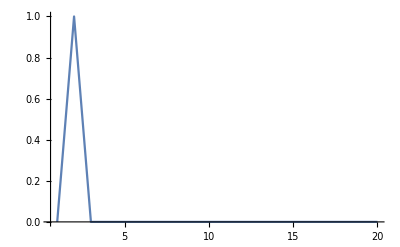

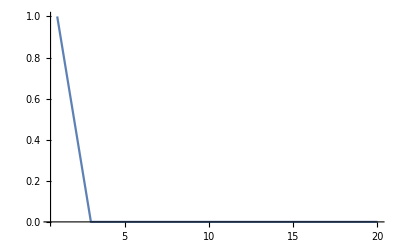

```mathematica
With[{n=20},
Solve[eqsNPL[n]/.Table[Subscript[G, i]->1,{i,n}]/.Table[Subscript[P, i]->If[i==1,1,0],{i,n}],varsNP[n]]
];
ListPlot[(Table[Subscript[a, i],{i,1,20}]/.%)[[1]]//N,Joined->True,PlotRange->All]
ListPlot[(Table[Subscript[u, i],{i,1,20}]/.%%)[[1]]//N,Joined->True,PlotRange->All]
```

```mathematica
With[{n=1},
Solve[eqsNPL[n]/.Table[Subscript[G, i]->1,{i,n}]/.Table[Subscript[P, i]->If[i==1,1,0],{i,n}],varsNP[n]]
]
```

{{a_1→0,b_1→0,u_1→1,v_1→1}}

```mathematica
With[{n=3},
Solve[eqsNP2J[n]/.Table[Subscript[G, i]->1,{i,n}]/.Table[Subscript[P, i]->If[i==1,1,0],{i,n}],varsNP[n]]
]
```

{{a_1→-4/3,a_2→2/3,a_3→2/3,b_1→-4/3,b_2→2/3,b_3→2/3,u_1→1/3,u_2→1/3,u_3→1/3,v_1→1/3,v_2→1/3,v_3→1/3}}

```mathematica
With[{n=3,j=2},Module[{s},
s=Solve[eqsNPL[n]/.Table[Subscript[G, i]->1,{i,n}]/.Table[Subscript[P, i]->If[i==j,1,0],{i,n}],varsNP[n]];
{
(Table[Subscript[u, i],{i,n}]/.s)[[1]],
(Table[Subscript[v, i],{i,n}]/.s)[[1]],
(Table[Subscript[a, i],{i,n}]/.s)[[1]],
(Table[Subscript[b, i],{i,n}]/.s)[[1]]
}
]]
%//Transpose
```

{{0,1/2,1/2},{1/2,1/2,0},{0,-1,1},{1,-1,0}}

{{0,1/2,0,1},{1/2,1/2,-1,-1},{1/2,0,1,0}}

## Failed test

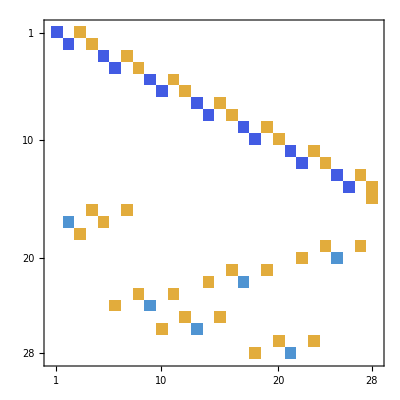

{0.,0.5,0.,1.,0.5,0.5,-1.,-1.,0.5,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
A={{-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-2.0,0.0,1.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.0},{0.0,0.0,0.0,1.0,0.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,-1.0,0.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.0,0.0,0.0,1.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.0,0.0,0.0,-1.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.0,0.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.0,0.0,0.0,-1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.0,0.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,1.0,0.0,0.0,-1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.0,0.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.0,0.0,0.0,-1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.0,0.0,0.0,1.0,0.0,0.0,0.0,0.0,0.0},{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.0,0.0,0.0,-1.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0}};
b={-0.0,-0.0,-2.0,-2.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};
MatrixPlot[A]
LinearSolve[A,b]
```

```mathematica
LUDecomposition[A]
%[[1]]//MatrixForm
```

{{{-2.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-2.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-2.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-2.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.5,0.,-0.5,-0.5,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.5,0.,0.5,0.5,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.5,0.,0.5,0.5,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.5,0.,0.5,0.5,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.5,0.,0.5,0.5,0.,-1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.,0.,1.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.5,0.,0.5,0.5,0.,-1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}},{1,2,18,16,3,4,17,23,5,6,24,25,7,8,26,21,9,10,22,27,11,12,28,19,13,14,20,15},7.5}

(-2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.5 | 0. | -0.5 | -0.5 | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.5 | 0.5 | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.5 | 0.5 | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.5 | 0.5 | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.5 | 0.5 | 0. | -1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.5 | 0.5 | 0. | -1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
Solve[{
q1a==2g1(p1a-e1),
q1b==2g1(p1b-e1),
q2a==2g2(p2a-e2),
q2b==2g2(p2b-e2),
q3a==2g3(p3a-e3),
q3b==2g3(p3b-e3),
q1a==0,
q2b==0,
q3b==0,
q1b+q2a+q3a==0,
p1b==p2a,p2a==p3a
},
{
q1a,q1b,q2a,q2b,q3a,q3b,
p1a,p1b,p2a,p2b,p3a,p3b
}]
```

{{q1a→0,q1b→-(2 (e1 g1 g2-e2 g1 g2+e1 g1 g3-e3 g1 g3))/(g1+g2+g3),q2a→-(2 (-e1 g1 g2+e2 g1 g2+e2 g2 g3-e3 g2 g3))/(g1+g2+g3),q2b→0,q3a→-(2 (-e1 g1 g3+e3 g1 g3-e2 g2 g3+e3 g2 g3))/(g1+g2+g3),q3b→0,p1a→e1,p1b→-(-e1 g1-e2 g2-e3 g3)/(g1+g2+g3),p2a→-(-e1 g1-e2 g2-e3 g3)/(g1+g2+g3),p2b→e2,p3a→-(-e1 g1-e2 g2-e3 g3)/(g1+g2+g3),p3b→e3}}

## Through-flow

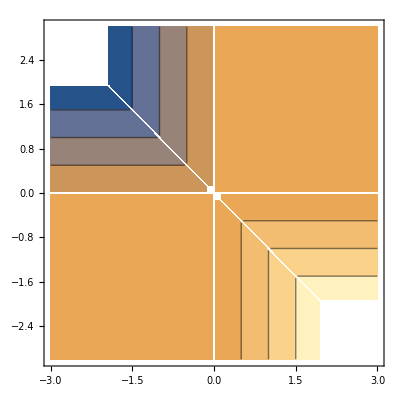

```mathematica
through[a_,b_]:=Min[Max[a,-b],0]+Max[Min[a,-b],0]
ContourPlot[through[a,b],{a,-3,3},{b,-3,3}]
```